# Chapter6: Scalable Multi-Beam focusing in Modular Clustered Optical Apertures Supplementary Material: Numerical Simulations

## Abstract :

Optical wireless networks emerge as a promising solution to the ever-growing data demand for user-centric indoor applications. This work demonstrates a novel approach to advance multi-user radiation patterns in indoor optical wireless networks by utilizing a cluster-based optical aperture comprising IR radiative elements. Spatially distributed IR clusters permit a non-uniform spherical wave model to focus the radiation in the near-field regime. By executing sub-clusters within main clusters and assigning them to groups for phase delay compensation, we ensure the generation of independent narrow beams focused on each receiver simultaneously. To mitigate the grating lobe formation, we incorporate a dual-carrier framework that introduces an effective wavelength for the system. Based on this theoretical model, we examine multi-beam focusing with a systematic arrangement of clusters on a planar ceiling. It follows a phased array within a phased array structure and incorporates a sub-cluster segmentation algorithm. We suggest optimizing cluster excitation based on receiver positions to enhance power efficiency and safety. This involves selecting the optimal clusters from a uniform array by solving a multiobjective non-convex binary optimization problem, aiming to maximize receiver intensity, minimize intensity variations, and reduce side lobes level. Instead of stochastic algorithms, we adopt a sparse relaxation-based weighted sum method that convexifies the binary space with L1 norm regularization compensating for convexity. The Transformed problem is solved deterministically via Nelder-Mead simplex without gradients. Simulated results confirm a better multi-beam focusing pattern, effectively balancing three objectives. Our findings pave the way for sustainable indoor optical wireless networks in next-generation communication.

## Initialization and styling

```mathematica
ClearAll["Global`*"](*Clear Variables and memory*)
```

Define Colors :

```mathematica
c0=RGBColor[10/255,50/255,100/255];   (*Very Dark Blue*)
c1=RGBColor[12/255,54/255,105/255];
c2=RGBColor[14/255,58/255,110/255];
c3=RGBColor[16/255,62/255,115/255];
c4=RGBColor[18/255,66/255,120/255];
c5=RGBColor[20/255,70/255,130/255];   (*Dark Blue*)
c6=RGBColor[22/255,74/255,135/255];
c7=RGBColor[24/255,78/255,140/255];
c8=RGBColor[26/255,82/255,145/255];
c9=RGBColor[28/255,86/255,150/255];
c10=RGBColor[30/255,90/255,160/255];  (*Medium-Dark Blue*)
c11=RGBColor[34/255,98/255,165/255];
c12=RGBColor[38/255,106/255,170/255];
c13=RGBColor[42/255,114/255,175/255];
c14=RGBColor[46/255,118/255,180/255];
c15=RGBColor[52/255,124/255,184/255];  (*Medium Blue*)
c16=RGBColor[56/255,132/255,188/255];
c17=RGBColor[60/255,140/255,192/255];
c18=RGBColor[64/255,148/255,196/255];
c19=RGBColor[68/255,152/255,200/255];
c20=RGBColor[90/255,160/255,210/255];  (*Light-Medium Blue*)
c21=RGBColor[100/255,170/255,215/255];
c22=RGBColor[110/255,180/255,220/255];
c23=RGBColor[120/255,185/255,225/255];
c24=RGBColor[130/255,190/255,230/255]; (*Light Blue*)
c25=RGBColor[140/255,195/255,233/255];
c26=RGBColor[150/255,200/255,235/255];
c27=RGBColor[160/255,205/255,238/255];
c28=RGBColor[170/255,215/255,245/255]; (*Very Light Blue*)
c29=RGBColor[185/255,190/255,220/255];
c30=RGBColor[200/255,160/255,195/255];
c31=RGBColor[210/255,150/255,185/255];
c32=RGBColor[225/255,160/255,195/255];
c33=RGBColor[230/255,165/255,185/255];
c34=RGBColor[235/255,175/255,175/255]; (*Light Red-Purple*)
c35=RGBColor[240/255,150/255,160/255];
c36=RGBColor[245/255,130/255,150/255];
c37=RGBColor[245/255,130/255,140/255];
c38=RGBColor[245/255,130/255,130/255];
c39=RGBColor[245/255,130/255,120/255]; (*Light Red*)
c40=RGBColor[235/255,120/255,110/255];
c41=RGBColor[230/255,110/255,100/255];
c42=RGBColor[225/255,105/255,95/255];
c43=RGBColor[220/255,100/255,90/255];  (*Medium Red*)
c44=RGBColor[210/255,90/255,80/255];
c45=RGBColor[200/255,80/255,70/255];
c46=RGBColor[190/255,70/255,60/255];   (*Dark Red*)
c47=RGBColor[170/255,60/255,50/255];
c48=RGBColor[150/255,50/255,40/255];
c49=RGBColor[130/255,40/255,30/255];
c50=RGBColor[100/255,30/255,20/255];
```

## Numerical Simulations

### Defining functional and dimensional parameters

Functional parameters for the dual carrier framework

```mathematica
λd = 1.56*10^-6; (*data wavelength*)
wavelengthDiff =4*1.2*10^-12; 
λb = λd - wavelengthDiff; (*baseline wavelength*)
λe =2*(λd*λb)/(λd - λb);(*effective wavelength*)
```

Dimensional parameters of an indoor room

```mathematica
xLength=3;
yLength=4;
zHeight=3;
xMiddle=Round[xLength]/2;
yMiddle=Round[yLength]/2;
```

Dimensional parameters of optical cluster aperture of IR radiative elements

```mathematica
mx1=6; (*Cluster count along x axis*)
my1=8;(* Cluster count along y axis*)
nx1=6;(*IR elements in a cluster along x axis*)
ny1=6;(*IR elements in a cluster along y axis*)
```

```mathematica
Dis1=0.5;(* Distance between IR clusters is 0.5 m*)
dis1=λd/2;(* Distnace between nano radiating elements is half of the IR wavelength*)
```

### Multi-Beam focusing pattern of the proposed planar optical aperture

Define the sub-cluster segmentation algorithm

```mathematica
selectValidSubMatrixDimension[matrixRowCount_,matrixColCount_,subMatrixCount_]:=Module[{totalElems,subMatrixSize,possibleRowDimensions,r,c,validDimensions,mostSquareDimension},
totalElems=matrixRowCount*matrixColCount;
subMatrixSize=totalElems/subMatrixCount;
(*Find possible Row dimensions for the calculated submaitrxSize*)
possibleRowDimensions=Select[Divisors[subMatrixSize],Divisible[matrixRowCount,#]&];
(*find matching Column Size for the Possible Row Dimensions and then select possible couples which can accomadate subMatrix by finindg correct column sizes*)
validDimensions=Select[Table[{r,c=subMatrixSize/r},{r,possibleRowDimensions}],Divisible[matrixColCount,#[[2]]]&];
(*Select MSot squarer pairs and if there are tow select low row count with high col count*)
mostSquareDimension=MinimalBy[validDimensions,Abs[#[[1]]-#[[2]]]&];
(*If[Length[mostSquareDimension]>=1, Return[mostSquareDimension[[1]]],Return[mostSquareDimension]]*);
Return[mostSquareDimension[[1]]];
]
```

```mathematica
subdividingMatrix[uElems_,vElems_,userCount_]:=Module[{factors,nearestFactor,subMatrixDimension,matrix,r,c,u,v,m,n},
factors=Divisors[uElems*vElems];
(*Finding nearest factor for the given number of users*)
nearestFactor=SelectFirst[factors,#>=userCount&];
(*Find the best submatrix dimension for the given number of users*)
subMatrixDimension=selectValidSubMatrixDimension[uElems,vElems,nearestFactor];
subMatrixDimension
]
```

Define the multi-beam focusing pattern with dual carrier framework

```mathematica
beamFocusingPatternPlanar[λd_ ,λe_,x_,y_,z_,Dis_,dis_,mxClus_,myClus_,nxElems_,nyElems_,xMid_,yMid_,focalPoints_]:=Module[{arbitraryPoint,elementPoint,nx,ny,mx,my,clusterMidPoint,rt,rp,focalPointCount,subMatrixDim,r,c,m,n,assignedSubMatrices,beamFocusingPlanarCluster,rpI,deltaArrI},
arbitraryPoint={x,y,z};
elementPoint={xMid+(dis/2*(2*nx-nxElems-1)+Dis/2*(2*mx-mxClus-1)),yMid+(dis/2*(2*ny-nyElems-1)+Dis/2*(2*my-myClus-1)),zHeight};
clusterMidPoint={xMid+Dis/2*(2*mx-mxClus-1),yMid+Dis/2*(2*my-myClus-1),zHeight};
rt=EuclideanDistance[arbitraryPoint,clusterMidPoint];
rp=EuclideanDistance[arbitraryPoint,elementPoint];
focalPointCount=Length[focalPoints];
subMatrixDim=subdividingMatrix[nxElems,nyElems,focalPointCount];
r=subMatrixDim[[1]];
c=subMatrixDim[[2]];
assignedSubMatrices=1;
beamFocusingPlanarCluster=0;
For[m=1,m<=nxElems,m+=r,{
For[n=1,n<=nyElems,n+=c,{
If[assignedSubMatrices>focalPointCount,Break[],];
rpI=EuclideanDistance[focalPoints[[assignedSubMatrices]],elementPoint];
deltaArrI=rp-rpI;
beamFocusingPlanarCluster+=∑_(nx=m)^(m+r-1) ∑_(ny=n)^(n+c-1) (Cos[(2π)/λe*deltaArrI]*Exp[-ⅈ*(2π)/λd*deltaArrI])/rt;
assignedSubMatrices++;
}]
}];
Table[beamFocusingPlanarCluster,{mx,1,mxClus},{my,1,myClus}]
]
```

#### Normalized intensity pattern for 2 receivers : Figure 05

Plotting the normalized beam intensity patterns

```mathematica
maxRadiationY[ymin_,ymax_,yres_,radiation_]:=Module[{tempy},
tempy=Table[{Abs[radiation]},{y,ymin,ymax,yres}];
Max[tempy]
]
```

```mathematica
myColorFunction=Function[{z},Which[z<=-25,c0,z<=-24.5,c1,z<=-24,c2,z<=-23.5,c3,z<=-23,c4,z<=-22.5,c5,z<=-22,c6,z<=-21.5,c7,z<=-21,c8,z<=-20.5,c9,z<=-20,c10,z<=-19.5,c11,z<=-19,c12,z<=-18.5,c13,z<=-18,c14,z<=-17.5,c15,z<=-17,c16,z<=-16.5,c17,z<=-16,c18,z<=-15.5,c19,z<=-15,c20,z<=-14.5,c21,z<=-14,c22,z<=-13.5,c23,z<=-13,c24,z<=-12.5,c25,z<=-12,c26,z<=-11.5,c27,z<=-11,c28,z<=-10.5,c29,z<=-10,c30,z<=-9.5,c31,z<=-9,c32,z<=-8.5,c33,z<=-8,c34,z<=-7.5,c35,z<=-7,c36,z<=-6.5,c37,z<=-6,c38,z<=-5.5,c39,z<=-5,c40,z<=-4.5,c41,z<=-4,c42,z<=-3.5,c43,z<=-3,c44,z<=-2.5,c45,z<=-2,c46,z<=-1.5,c47,z<=-1,c48,z<=-0.5,c49,True,c50]];
```

```mathematica
tickFormat[min_,max_,step_]:=Table[{i,NumberForm[N[i],{3,1}]},{i,min,max,step}];
```

```mathematica
plotPlanarRadiationXY[data_,fontSize_]:=Module[{normalizedPlot},
normalizedPlot=ListContourPlot[data,ContourStyle->None,Contours->50,ColorFunction->myColorFunction,ColorFunctionScaling->False,FrameLabel->{{" y axis (m)",None},{" x axis (m)",None}},LabelStyle->Directive[Black,fontSize,FontFamily->"Times"],PlotLegends->BarLegend[{Automatic,{-25,1}},50,LegendMarkerSize->{Automatic,360},LabelStyle->Directive[Black,fontSize,FontFamily->"Times"]],PlotLabel->Style["Normalized Intensity dB ",fontSize,Black,FontFamily->"Times"],FrameTicks->{{tickFormat[0,4,0.5],None},{tickFormat[0,3,0.5],None}},PlotRange->All,ImageSize->{360,400}]
]

zoomplotPlanarRadiationXY[data_]:=Module[{normalizedPlot},
normalizedPlot=ListContourPlot[data,ContourStyle->None,Contours->50,ColorFunction->myColorFunction,ColorFunctionScaling->False,LabelStyle->Directive[Black,14,FontFamily->"Times"],PlotRange->All,ImageSize->{200,220}]
]
```

Define receiver positions in the room

```mathematica
userLocations1={{1.6,2.3,0.75},{2.5,0.8,0.75}};(*for receiver Subscript[R, 1] and receiver Subscript[R, 2] repectively*)
```

Generating normalized intensity pattern for 2 users

```mathematica
radiationXY1=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations1],2]];
datapair1=ParallelTable[radiationXY1,{x,0,xLength,0.1},{y,0,yLength,0.1}];
dataPair1Max=Max[datapair1];
```

```mathematica
plotDataPair1=Flatten[ParallelTable[{x,y,20*Log[10,radiationXY1/dataPair1Max]},{x,0,xLength,0.05},{y,0,yLength,0.05}],1];
normalizedPlot1=plotPlanarRadiationXY[plotDataPair1,15];
```

```mathematica
plotAnnotations1=Graphics[{EdgeForm[{Dashed,RGBColor[0.6,0.6,0.6]}],(*Outline style for the rectangle*)FaceForm[None],Rectangle[{userLocations1[[1,1]]-0.25,userLocations1[[1,2]]-0.25},{userLocations1[[1,1]]+0.25,userLocations1[[1,2]]+0.25}],Rectangle[{userLocations1[[2,1]]-0.25,userLocations1[[2,2]]-0.25},{userLocations1[[2,1]]+0.25,userLocations1[[2,2]]+0.25}]}];
```

Normalized intensity main plot

```mathematica
mainPlotWithAnnotations=Show[normalizedPlot1,plotAnnotations1]
```

-Graphics-

Normalized intensity Zoomed plot at receiver 1

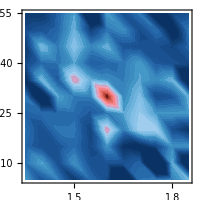

```mathematica
zoomDataPair1=Flatten[ParallelTable[{x,y,20*Log[10,radiationXY1/dataPair1Max]},{x,userLocations1[[1,1]]-0.25,userLocations1[[1,1]]+0.25,0.05},{y,userLocations1[[1,2]]-0.25,userLocations1[[1,2]]+0.25,0.05}],1];
zoomplot1=zoomplotPlanarRadiationXY[zoomDataPair1]
```

Normalized intensity Zoomed plot at receiver 2

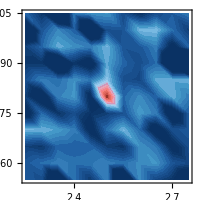

```mathematica
zoomDataPair2=Flatten[ParallelTable[{x,y,20*Log[10,radiationXY1/dataPair1Max]},{x,userLocations1[[2,1]]-0.25,userLocations1[[2,1]]+0.25,0.05},{y,userLocations1[[2,2]]-0.25,userLocations1[[2,2]]+0.25,0.05}],1];
zoomplot2=zoomplotPlanarRadiationXY[zoomDataPair2]
```

```mathematica
mainPlotInset=Rasterize[mainPlotWithAnnotations,"Image",ImageResolution->500];
zoomplot1Inset=Rasterize[zoomplot1,"Image",ImageResolution->500];
zoomplot2Inset=Rasterize[zoomplot2,"Image",ImageResolution->500];

finalFigure=Graphics[{Inset[mainPlotInset,{0.5,0.70},Center,{0.78,0.58}](*Object, position, alignment,size*),Inset[zoomplot1Inset,{0.30,0.25},Center,{0.32,0.26}],Inset[zoomplot2Inset,{0.62,0.25},Center,{0.32,0.26}],Dashed,GrayLevel[0.35],Thickness[0.002],Line[{{0.21,0.36},{0.45,0.75}}](*{x1,y1},{x2,y2}*),Line[{{0.41,0.36},{0.49,0.72}}],Line[{{0.53,0.36},{0.58,0.55}}],Line[{{0.73,0.37},{0.65,0.57}}]},PlotRange->{{0.02,0.98},{0.08,1}},ImageSize->650,Background->White]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap6Fig5.pdf"}],Rasterize[Show[finalFigure],"Image",ImageResolution->600]];
```

#### Normalized beam focusing pattern for 2 receivers: figure 06

Plotting the normalized beam focusing  patterns

```mathematica
plotRadiationY[dataPair_,yMin_,yMax_,axisLabel_,location_,user_]:=Module[{labelSpot,specialTick,normalizedPlot},
If[axisLabel=="y-axis (m)",{specialTick=location[[2]],
If[location[[2]]>=2.5,labelSpot={0.7,0.9},labelSpot={3.3,0.9}]}
,{specialTick=location[[1]],If[location[[1]]>=2.5,labelSpot={0.7,0.9},labelSpot={2.5,0.9}]}];
normalizedPlot=ListLinePlot[dataPair,PlotRange->{{yMin,yMax},{0,1}},AxesOrigin->{0,0},Frame->{{True,False},{True,False}},PlotStyle->Directive[Thickness[0.006],RGBColor[0.70,0.28,0.05]],LabelStyle->Directive[Black,14,FontFamily->"Times New Roman"],FrameLabel->{axisLabel,"ψ (r)"},Epilog->{Text[Style[Row[{Subscript["R",user],": ("<>StringJoin[Riffle[ToString/@location,", "]]<>")"}],FontFamily->"Times New Roman",FontSize->14],labelSpot]},FrameTicks->{Join[Table[If[Mod[i,1]==0,{i,ToString[i]<>".0"},{i,i}],{i,yMin,yMax,1}],{{specialTick,Style[ToString[specialTick],FontFamily->"Times New Roman",FontSize->14,RGBColor[1,0.5,0.5]]}}],Automatic},ImageSize->{400,250},AspectRatio->Full,GridLines->{{},{{1,Dashed}}},GridLinesStyle->Directive[Black,Dashed,Thickness[0.005]]]
]
```

```mathematica
radiationAlongX[user_,userLocations_,max_]:=Module[{radiationWithX,radiationWithXtr,dataPoints,dataValues,dataValuesMax,dataPair},
radiationWithX=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,userLocations[[user,2]],0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations],2]];
radiationWithXtr=radiationWithX/.x->y;
dataPoints=Table[y,{y,0,xLength,0.001}];
dataValues=Table[radiationWithXtr,{y,0,xLength,0.001}];
dataValuesMax=Max[dataValues];
dataPair=Transpose[{dataPoints,dataValues/max}];
plotRadiationY[dataPair,0,xLength,"x-axis (m)",userLocations[[user]],user]
]
```

```mathematica
radiationAlongY[user_,userLocations_,max_]:=Module[{radiationWithY,dataPoints,dataValues,dataValuesMax,dataPair},
radiationWithY=Abs[Total[beamFocusingPatternPlanar[λd,λe,userLocations[[user,1]],y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations],2]];
dataPoints=Table[y,{y,0,yLength,0.001}];
dataValues=Table[radiationWithY,{y,0,yLength,0.001}];
dataValuesMax=Max[dataValues];
dataPair=Transpose[{dataPoints,dataValues/max}];
plotRadiationY[dataPair,0,yLength,"y-axis (m)",userLocations[[user]],user]
]
```

Subfigure a: Normalized beam focusing pattern along x-axis at y = 2.3

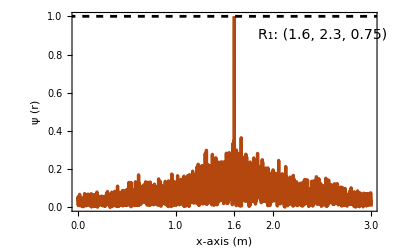

```mathematica
crosSecPlot1=radiationAlongX[1,userLocations1,dataPair1Max]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap6Fig6a.pdf"}],Rasterize[Show[crosSecPlot1],"Image",ImageResolution->600]];
```

Subfigure b: Normalized beam focusing pattern along y-axis at  x = 1.6

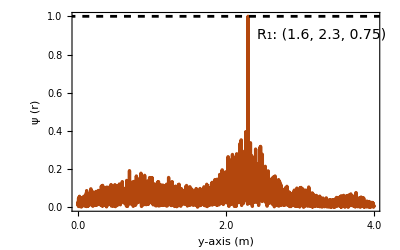

```mathematica
crosSecPlot2=radiationAlongY[1,userLocations1,dataPair1Max]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap6Fig6b.pdf"}],Rasterize[Show[crosSecPlot2],"Image",ImageResolution->600]];
```

Subfigure c: Normalized beam focusing pattern along x-axis at  y = 0.8

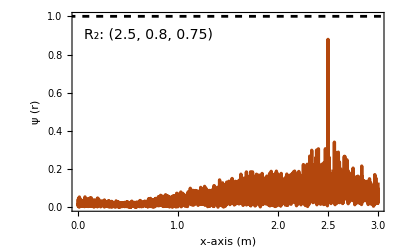

```mathematica
crosSecPlot3=radiationAlongX[2,userLocations1,dataPair1Max]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap6Fig6c.pdf"}],Rasterize[Show[crosSecPlot3],"Image",ImageResolution->600]];
```

Subfigure d: Normalized beam focusing pattern along y-axis at  x = 2.5

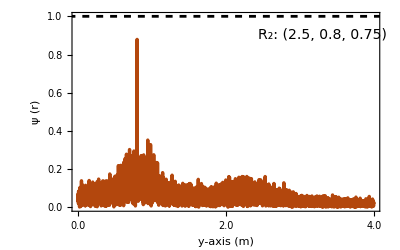

```mathematica
crosSecPlot4=radiationAlongY[2,userLocations1,dataPair1Max]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap6Fig6d.pdf"}],Rasterize[Show[crosSecPlot4],"Image",ImageResolution->600]];
```

#### Finding peak side lobe level (PSLL) for the given 2 receiver configuration

Defining PSLL

```mathematica
findPlanarSLL[focalPoints_,maxBeamVal_,clusterExcitationPattern_]:=Module[{locationList,i,radiationList,maxPair={},maxPairList={},maxSll,maxInt,psll,psllLocation},
For[i=1,i<=Length[focalPoints],i++,
locationList=DeleteCases[Flatten[Table[{x,y},{x,focalPoints[[i,1]]-0.5,focalPoints[[i,1]]+0.5,0.05},{y,focalPoints[[i,2]]-0.5,focalPoints[[i,2]]+0.5,0.05}],1],{x_,y_}/;((focalPoints[[i,1]]-0.005<=x<= focalPoints[[i,1]]+0.005) && (focalPoints[[i,2]]-0.005<=y<= focalPoints[[i,2]]+0.005))];
radiationList =ParallelTable[{Total[beamFocusingPatternPlanar[λd,λe,locationList[[j,1]],locationList[[j,2]],0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,focalPoints]*clusterExcitationPattern,2],{locationList[[j,1]],locationList[[j,2]]}},{j,1,Length[locationList]}]; 
maxPair=First@MaximalBy[radiationList,Abs[First[#]]&];
AppendTo[maxPairList,maxPair]
] ;
maxInt=Abs[maxBeamVal];
maxSll=First@MaximalBy[maxPairList,Abs[First[#]]&];
psll=20*Log10[Abs[maxSll[[1]]]/maxInt];
psllLocation={maxSll[[2]][[1]],maxSll[[2]][[2]],0.75};
{psll,psllLocation}
];
```

Find PSLL for given R_1 and R_2 receivers

```mathematica
fullExcitationPattern=fullExcitationPattern=ConstantArray[1,{mx1,my1}];
psllResult1=findPlanarSLL[userLocations1,dataPair1Max,fullExcitationPattern];
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[psllResult1[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],Round[#,0.01]&/@psllResult1[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

PSLL Value   : | -9.12 dB
PSLL Location : | {1.5,2.35,0.75}

#### Evaluating Max-Min Power Ratio (MMPR) in a Two-Receiver System Under Varying Detector Area.

```mathematica
beamPower[config_,userlocation_,detectorArea_]:=Module[{x0,x1,y0,y1,beamPower,η=377,α=1},
x0=userlocation[[1]]-detectorArea/2;
x1=userlocation[[1]]+detectorArea/2;
y0=userlocation[[2]]-detectorArea/2;
y1=userlocation[[2]]+detectorArea/2;
beamPower=α/(2*η)*Quiet[NIntegrate[(config)^2,{x,x0,x1},{y,y0,y1}]]
];
```

```mathematica
beamPowerForUsers[config_,userLocations_,detectorArea_]:=Module[{beamPrList={},j,beamPr},
For[j=1,j<=Length[userLocations],j++,
beamPr=beamPower[config,userLocations[[j]],detectorArea];
AppendTo[beamPrList,beamPr];
];
beamPrList
];
```

```mathematica
mmprCal[radiationXY_,userLocations_]:=Module[{relativePowerList={},i,beamPrList={}},
For[i=1,i<=10,i++,
beamPrList=beamPowerForUsers[radiationXY,userLocations,i*10^-3];
AppendTo[relativePowerList,Min[beamPrList]/Max[beamPrList]];
];
relativePowerList
];
```

Finding MMPR for R_1 and R_2 receivers while changing the detector area:Figure 07

```mathematica
(*userPowerList1=mmprCal[radiationXY1,userLocations1];*)
detectorAreaList={1,4,9,16,25,36,49,64,81,100};
```

```mathematica
userPowerList1={0.7983443100282904,0.7929469867492019,0.7875317945555133,0.8015082428835079,0.7774486680150762,0.810837955334769,0.7968581510982969,0.7797753916570314,0.7796131874625148,0.7780511620289495};
```

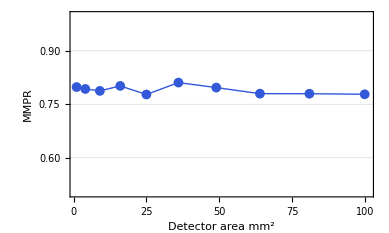

```mathematica
mmprFig=ListLinePlot[Transpose[{detectorAreaList,userPowerList1}],PlotMarkers->{"●",10},(*Adds dots at the points*)PlotStyle->Directive[RGBColor[0.2,0.35,0.85],Thick],Frame->True,FrameStyle->{Black,None,Black,None},FrameLabel->{Style["Detector area mm^2",FontFamily->"Times",FontSize->14,Black],Style[" MMPR ",FontFamily->"Times",FontSize->14,Black]},FrameTicksStyle->Directive[Black,FontSize->12,FontFamily->"Times New Roman"],GridLines->{None,Automatic},GridLinesStyle->Directive[Dashed,Gray],PlotRange->{{0.75,101},{0.5,1}},AspectRatio->0.6,ImagePadding->{{40,20},{40,20}} (*Prevents clipping*)]
```

```mathematica
Mean[userPowerList1]*100
```

79.0292

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap6Fig7.pdf"}],Rasterize[mmprFig,"Image",ImageResolution->600]];
```

### Find selective Cluster Excitation pattern using sparse relaxation-based weighted sum algorithm

#### Defining the sparse relaxation based MOO algorithm (SR)

consider same receiver locations of R_1 and R_2 inside the same indoor room setup.

```mathematica
userLocations2={{1.6,2.3,0.75},{2.5,0.8,0.75}};
```

Define the algorithm parameters

```mathematica
maxIterations=5;(* iteration count for algorithm execution *)
```

Define sparse relaxation-based weighted sum algorithm with L_1 norm regularization.

```mathematica
clusterThinningAlgo[userLocations_,onCount_,weightCom_]:=Module[{radiationAtUseri={},i,j,modRadiationListForUsers={},weights,vars,val=0,valSet={},xyList={},objectiveFunction=0,radiationData ,sllDataSet={},sllData=0,thresholdIntensityL,thresholdIntensityU,mMin=6,mMax=40,constraints,solution,extractedSolution,previousSolution,sortedSolution,finalSolution,optVal, optValSet={},optSllData},

weights=ConstantArray[1,mx1*my1];(*Initialize the weight matrix with all values set to 1 *)
vars=Array[b,mx1*my1];(*Initialize the matrix H with unknowns *)

(*Find intensities at user locations*)
For[i=1,i<=Length[userLocations],i++,
radiationAtUseri=beamFocusingPatternPlanar[λd,λe,userLocations[[i,1]],userLocations[[i,2]],0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations];
AppendTo[modRadiationListForUsers,Flatten[radiationAtUseri,1]];
];
For[i=1,i<=Length[userLocations],i++,
{val=Abs[modRadiationListForUsers[[i]].vars]^2,
AppendTo[valSet,val]}
];

(*Find PSLL*)
For[i=1,i<=Length[userLocations],i++,
xyList=DeleteCases[Flatten[Table[{x,y},{x,userLocations[[i,1]]-0.5,userLocations[[i,1]]+0.5,0.1},{y,userLocations[[i,2]]-0.5,userLocations[[i,2]]+0.5,0.1}],1],{x_,y_}/;((userLocations[[i,1]]-0.005<=x<= userLocations[[i,1]]+0.005) && (userLocations[[i,2]]-0.005<=y<= userLocations[[i,2]]+0.005))];
radiationData =ParallelTable[Flatten[beamFocusingPatternPlanar[λd,λe,xyList[[j,1]],xyList[[j,2]],0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations],1],{j,1,Length[xyList]}]; 
sllData=Max[Abs[radiationData.vars]^2];
AppendTo[sllDataSet,sllData];
] ;

(*objective statement with Subscript[L, 1] norm regularization. Considered the weighted sum of three objectives: maximizing intensity at receiver locations, minimizing intensity variation, minimizing peak side lobe level*)
objectiveFunction=weightCom[[1]]*Mean[valSet]-weightCom[[2]]*StandardDeviation[valSet]-weightCom[[3]]*Max[sllDataSet]-1/onCount*(weights.vars);
thresholdIntensityL=0.9*1/Length[userLocations]*((mMin*nx1*ny1)/EuclideanDistance[{xMiddle,yMiddle,zHeight},{xLength,yLength,0}])^2;(*Lower intensity threshold*)
thresholdIntensityU=1.1*1/Length[userLocations]*((mMax*nx1*ny1)/EuclideanDistance[{xMiddle,yMiddle,zHeight},{xMiddle,yMiddle,0}])^2;(*Upper intensity threshold*)

constraints={0<=vars<=1,Total[vars]==onCount,Table[thresholdIntensityL<=valSet[[i]]<=thresholdIntensityU,{i,1,Length[userLocations]}]};(*Constraints to consider*)

extractedSolution=Array[0,mx1*my1];
previousSolution=Array[0,mx1*my1];
(*Perform Nelder-Mead simplex method on the transformed objective statment in iterative manner*)
For[i=1,i<=maxIterations,i++,
previousSolution=extractedSolution;
solution=NMaximize[{objectiveFunction,constraints},vars,Method->"NelderMead"];
(*Extract the solution : Numerical solutions for variables*)
extractedSolution=Values[solution[[2]]]; 

(*Update weights for the next iteration*)
weights=1-extractedSolution/Max[extractedSolution];

(*Check for convergence*)
If[Norm[extractedSolution-previousSolution,Infinity]<10^-3,Break[],]; 
];

(*Controlled rounding to enforce binary solution*);
sortedSolution=Sort[Thread[{extractedSolution,Range[mx1*my1]}],#1[[1]]>#2[[1]]&];
finalSolution=ConstantArray[0,mx1*my1]; (*Initialize all to 0 (inactive)*)
Do[finalSolution[[sortedSolution[[i,2]]]]=1,{i,1,onCount} ];(*Select top onCluster indices to be active (set to 1)*)

(*Check the objectives space for the finalized binary solution *)
For[i=1,i<=Length[userLocations],i++,
{optVal=Abs[modRadiationListForUsers[[i]].finalSolution]^2,
AppendTo[optValSet,optVal]}
];
optSllData=Max[Abs[radiationData.finalSolution]^2];

(*Return the solution*)
 {ArrayReshape[finalSolution,{mx1,my1}],Mean[optValSet],StandardDeviation[optValSet],optSllData}
]
```

#### Evaluating the Pareto Optimal behaviour for 3 objectives on different weight combinations

This for loop generates the objective space for 60 different weight combinations when only 18 IR radiative clusters are active. In each iteration, it computes the selective excitation pattern using the sparse-relaxation based weighted sum algorithm defined above. As a result, completing the loop will take a considerable amount of time.

```mathematica
onClusters=18;(*On cluster count*)
nCount=10;dataList={};
```

```mathematica
For[i=0,i<=nCount,i++ ,
For[j=0,j<=(nCount-i),j++,
{
k=nCount-i-j;
result={};
weightCombination={i/nCount,j/nCount,k/nCount};
result=clusterThinningAlgo[userLocations2,onClusters,weightCombination];
AppendTo[dataList,{weightCombination,result[[2]],result[[3]],result[[4]]}];
}
]
];
```

```mathematica
(*dataList={{{0,0,1},12317.163826192373,3125.5551641167317,1007.2965320650502},{{0,1/10,9/10},13622.423278111797,1727.8270973887963,1302.3353160555675},{{0,1/5,4/5},12894.902778790183,417.7132413195552,2179.056746497757},{{0,3/10,7/10},13092.94335934894,61.54654023164591,1506.8958635881854},{{0,2/5,3/5},12659.348175563515,15.506037559273214,1781.2307607555842},{{0,1/2,1/2},13374.291898857588,506.01931537689484,1515.3061493501382},{{0,3/5,2/5},13147.109596600334,197.52205013886115,1285.5330925615249},{{0,7/10,3/10},13368.652440143633,682.2507223698417,1995.852529334744},{{0,4/5,1/5},12855.186532766387,40.35252132002141,1582.9132537949815},{{0,9/10,1/10},13467.184943902797,1159.040665371768,1746.1473479853748},{{0,1,0},14943.660209314092,803.7107149512732,3844.235664911831},{{1/10,0,9/10},13909.46424213295,3039.241142326695,1413.3203815710037},{{1/10,1/10,4/5},13470.983906043486,1640.6310418172754,1457.1046552932446},{{1/10,1/5,7/10},14228.069040703438,143.42834192880724,1304.8123682867392},{{1/10,3/10,3/5},14212.568447698006,653.7698382625756,1725.1637037226797},{{1/10,2/5,1/2},14668.876782421848,729.4379789712634,1882.8479398758782},{{1/10,1/2,2/5},14668.876782421848,729.4379789712634,1882.8479398758782},{{1/10,3/5,3/10},14999.40081899811,304.0702244001078,1529.8824938165224},{{1/10,7/10,1/5},14844.240851982573,1419.7621968381354,1799.6179250054859},{{1/10,4/5,1/10},15612.720010652141,420.52054179714764,2002.0937649851235},{{1/10,9/10,0},16106.203607872249,220.5765493971064,3911.693627263705},{{1/5,0,4/5},14068.564256098529,2498.9820568212267,3047.3938451526205},{{1/5,1/10,7/10},14527.49969345067,141.71585292891027,1695.3644538190931},{{1/5,1/5,3/5},14945.35918946882,281.04931349699933,1378.179997759658},{{1/5,3/10,1/2},14993.120013534342,840.5157671404131,1514.7855535281374},{{1/5,2/5,2/5},14992.79630359555,788.4478113187528,1830.2051615073078},{{1/5,1/2,3/10},15222.940326502596,489.0590696240606,1791.4816703184647},{{1/5,3/5,1/5},15565.099524184403,140.91527854898612,2274.1064595334574},{{1/5,7/10,1/10},16129.341065300889,343.95615696467627,2455.613690300996},{{1/5,4/5,0},16341.571709189317,196.9916094404709,3027.2251539319204},{{3/10,0,7/10},14915.13486515912,1167.326136076252,1351.6613895342766},{{3/10,1/10,3/5},15275.283766877206,136.5002760454802,1166.1552223202223},{{3/10,1/5,1/2},15222.940326502596,489.0590696240606,1791.4816703184647},{{3/10,3/10,2/5},15041.758124962402,483.1592599055826,1799.7430662051527},{{3/10,2/5,3/10},15919.152469292336,111.17173099198435,1899.234454593112},{{3/10,1/2,1/5},15924.511723303443,202.40196816571793,2249.5821433894885},{{3/10,3/5,1/10},16222.106952597958,67.97500988701395,2661.8524359534827},{{3/10,7/10,0},16346.12075134799,112.53120734094658,3666.6241604734855},{{2/5,0,3/5},15427.066222522764,1748.854626826779,1630.4968486311577},{{2/5,1/10,1/2},15705.782844648847,1171.0996664483775,2218.7218075138294},{{2/5,1/5,2/5},15919.152469292336,111.17173099198435,1899.234454593112},{{2/5,3/10,3/10},15924.511723303443,202.40196816571793,2249.5821433894885},{{2/5,2/5,1/5},16054.7649115249,70.38064931109469,2546.279186125843},{{2/5,1/2,1/10},16222.106952597958,67.97500988701395,2661.8524359534827},{{2/5,3/5,0},16299.128450076514,256.9526209590403,3517.2123892454015},{{1/2,0,1/2},15652.915203572138,2075.67061128804,1802.4534566078669},{{1/2,1/10,2/5},15906.165521388188,410.33247570671483,1676.7709182739686},{{1/2,1/5,3/10},15993.142278924826,494.75823173803536,2450.0831135303333},{{1/2,3/10,1/5},16222.106952597958,67.97500988701395,2661.8524359534827},{{1/2,2/5,1/10},16222.106952597958,67.97500988701395,2661.8524359534827},{{1/2,1/2,0},16245.836847784274,507.3278958288233,3440.5112211434166},{{3/5,0,2/5},16201.590946664834,1605.5798439506198,2082.632036097343},{{3/5,1/10,3/10},16166.343609698246,764.7939009459426,2714.103150513992},{{3/5,1/5,1/5},16222.106952597958,67.97500988701395,2661.8524359534827},{{3/5,3/10,1/10},16269.148879591856,131.57423127463898,3229.5464794460977},{{3/5,2/5,0},16260.877492737862,427.3130315448337,3395.2961420522647},{{7/10,0,3/10},16201.590946664834,1605.5798439506198,2082.632036097343},{{7/10,1/10,1/5},16299.192736496176,651.6340886644896,3177.00883792003},{{7/10,1/5,1/10},16269.148879591856,131.57423127463898,3229.5464794460977},{{7/10,3/10,0},16299.128450076514,256.9526209590403,3517.2123892454015},{{4/5,0,1/5},16261.962567312234,1074.251478028044,2178.2128131729246},{{4/5,1/10,1/10},16379.193200155343,897.7812530118438,2739.6235669572684},{{4/5,1/5,0},16346.12075134799,112.53120734094658,3666.6241604734855},{{9/10,0,1/10},16379.193200155343,897.7812530118438,2739.6235669572684},{{9/10,1/10,0},16346.12075134799,112.53120734094658,3666.6241604734855},{{1,0,0},16386.930393871928,1377.246902479051,2840.1239796780346}};*)
```

```mathematica
normalizedObjective1=dataList[[All,2]]/Max[dataList[[All,2]]];
normalizedObjective2=dataList[[All,3]]/Max[dataList[[All,3]]];
normalizedObjective3=dataList[[All,4]]/Max[dataList[[All,4]]];
weightList=dataList[[All,1]];
```

```mathematica
combinedNormalizedObjectiveList=Transpose[{normalizedObjective1,normalizedObjective2,normalizedObjective3}];
specialPoint={0.9120292104894643,0.07734797110971665,0.35232309303418474};
specialPoint={0.9120292104894643,0.07734797110971665,0.358505595882};
posDatPoint=Position[combinedNormalizedObjectiveList,specialPoint];
```

```mathematica
selectedWeightCombination=Flatten[weightList[[posDatPoint[[1]]]],1];(* Selected weight combination for subsequent evaluations*)
```

```mathematica
selectedWeightCombination={1/5,1/5,3/5};
```

```mathematica
newCombinedNormalizedObjectiveList=DeleteCases[combinedNormalizedObjectiveList,specialPoint];
```

Objective space for all different weight combinations: Figure 08

```mathematica
plot3D=ListPointPlot3D[{newCombinedNormalizedObjectiveList,{specialPoint}},AxesLabel->{"I_μ(H, r_q)","","S(H,q)"},PlotStyle->{Directive[{Blue,PointSize[0.02]}],Directive[{Darker[Red],PointSize[0.02]}]},LabelStyle->Directive[Black,12,FontFamily->"Times New Roman"],Boxed->False,Axes->True,Method->{"AxesDuringInteraction","Locked"},ViewPoint->{1.5,3.4,0.6},Ticks->{Table[i,{i,0,1,0.2}],Table[i,{i,0,1,0.2}],Table[i,{i,0,1,0.2}]},PlotLabel->" Normalized objective space", AspectRatio->1,FaceGrids->{{-1,0,0},{0,-1,0},{0,0,-1}},PlotRange->{{0,1},{0,1},{0,1}}];
plotLabel=Graphics3D[Text[Style[ToString[Round[specialPoint,0.01]],FontSize->12,FontFamily->"Times New Roman",FontColor->Darker[Red]],specialPoint+{-0.1,0.02,-0.35}]];
```

```mathematica
plotLabel2=Graphics3D[{Darker[Red],Arrowheads[0.05],Thickness[0.005],Arrow[{specialPoint+{-0.03,0.02,-0.30},specialPoint}]}];
```

```mathematica
customLabel=Graphics3D[{Text[Style["I_σ(H, r_q)",FontSize->12,FontColor->Black,FontFamily->"Times New Roman"],{0.2,0.5,1}]}];
```

```mathematica
Show[plot3D,plotLabel,plotLabel2,customLabel]
```

-Graphics3D-

#### Find the selective cluster excitation pattern and evaluate their resulting beam focusing pattern for varying active cluster counts: figure 09 and table 2

```mathematica
weightCombination1={0.2,0.2,0.6};(*Selected weight combination from early section*)
```

For same R1 and R2 receivers locations, This loop generates cluster excitation pattern and corresponding PSLL and MMPR for varying cluster activation count from 6 to 40. As a result, completing the loop will take a considerable amount of time.

```mathematica
clusterExcitationPatternGen[mMin_,mMax_,userLocation_,weightCom_]:=Module[{i,results={},clusterExcitationPatterncX,thinnedClusterRadiationXY,datapairMax,lsllResult={},userPowerList={}},
For[i=mMin,i<=mMax,i++,
clusterExcitationPatterncX=clusterThinningAlgo[userLocation,i,weightCom][[1]];
thinnedClusterRadiationXY=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocation]*clusterExcitationPatterncX,2]];
datapairMax=Max[ParallelTable[thinnedClusterRadiationXY,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
lsllResult=findPlanarSLL[userLocation,datapairMax,clusterExcitationPatterncX];
userPowerList=beamPowerForUsers[thinnedClusterRadiationXY,userLocation,10*10^-3];
AppendTo[results,{clusterExcitationPatterncX,lsllResult,userPowerList}];
];
results
];
```

```mathematica
excitationPatternList=clusterExcitationPatternGen[6,40,userLocations2,weightCombination1]
```

```mathematica
(*excitationPatternList={{{{1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0}},{-3.3055074355876313,{2.35,0.7000000000000001,0.75}},{0.00003389963501788961,0.00003870668465943989}},{{{1,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0}},{-2.9392605992512886,{1.55,2.1999999999999997,0.75}},{0.00004115859307402993,0.00004402990086807675}},{{{1,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0},{0,1,1,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0}},{-3.6641567510123894,{2.65,1.,0.75}},{0.000047044256725630906,0.00005056051264418566}},{{{1,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0}},{-4.880657286758943,{1.8000000000000003,2.15,0.75}},{0.0000531497296474355,0.000056286389091221925}},{{{1,0,0,0,0,0,0,0},{0,0,1,1,0,1,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0}},{-5.171899046319293,{2.65,1.,0.75}},{0.00006267070007486504,0.000060021774724979204}},{{{1,0,0,1,0,0,0,0},{0,0,1,0,0,1,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,1,0,0,0},{0,0,0,1,0,0,0,0}},{-5.12168292121004,{1.4000000000000001,2.3,0.75}},{0.00006486772010955742,0.0000676235112265919}},{{{1,0,0,1,0,0,0,0},{0,0,1,1,0,1,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0}},{-6.124237671884449,{1.4500000000000002,2.15,0.75}},{0.00007431249581031133,0.00007232588343320918}},{{{1,0,0,1,0,0,0,0},{1,0,1,1,0,1,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,1,0,0,0},{0,0,0,1,0,0,0,0}},{-6.139349437535168,{2.2,0.55,0.75}},{0.00007886011017811384,0.00007621535732068709}},{{{1,0,0,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,1,0,0,0},{0,0,0,1,0,0,0,0}},{-5.8816055097141,{2.5,0.8500000000000001,0.75}},{0.00008271403008296218,0.00008472910437177673}},{{{1,0,0,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,1,0,0,0},{0,0,1,1,0,0,0,0}},{-5.501295190061731,{2.5,0.8500000000000001,0.75}},{0.00008983213179712641,0.0000913596694415699}},{{{1,0,1,1,0,0,0,0},{1,0,1,1,0,1,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,1,0,0,0},{0,1,1,1,0,0,0,0}},{-6.583434866042542,{2.35,1.1,0.75}},{0.00009677475472716152,0.00009479164416023503}},{{{1,0,0,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,1,1,0,0,0},{0,1,1,1,0,0,0,0}},{-5.576831135842033,{2.5,0.8500000000000001,0.75}},{0.00010189341465353046,0.00010708981672906699}},{{{1,0,1,1,0,0,0,0},{1,0,1,1,0,1,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{1,1,0,1,1,0,0,0},{0,1,1,1,0,0,0,0}},{-7.114609676581939,{1.8000000000000003,2.15,0.75}},{0.00010801364778354527,0.00011217417676791618}},{{{1,0,0,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,0,0,0},{1,0,1,1,0,0,0,0},{1,1,0,0,1,0,0,0},{1,1,1,1,0,0,0,0}},{-7.47999441064842,{1.6500000000000001,2.25,0.75}},{0.00011096415411979238,0.00011793911225416585}},{{{1,0,1,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,0,0,0,0}},{-8.32050968157407,{1.6500000000000001,2.25,0.75}},{0.00011633889337868033,0.00012258032334689376}},{{{1,0,1,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,1,0,0},{1,0,1,0,0,0,0,0},{1,1,0,0,1,0,0,0},{1,1,1,1,1,0,0,0}},{-8.726233270492344,{2.65,0.6000000000000001,0.75}},{0.0001237552206815263,0.00012424681525253836}},{{{1,0,1,1,0,0,0,0},{1,0,1,0,0,1,0,0},{1,1,1,0,0,1,0,0},{1,0,1,1,0,0,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,0,0,0}},{-7.722676739972973,{2.5,0.8500000000000001,0.75}},{0.00012844346402541694,0.0001337446239610075}},{{{1,1,1,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,1,0,0},{1,0,1,1,0,0,0,0},{1,1,0,0,1,0,0,0},{1,1,1,1,1,0,0,0}},{-7.622528020233029,{1.8000000000000003,2.25,0.75}},{0.00013769601038023625,0.00013306170068751156}},{{{1,1,1,1,0,0,0,0},{1,0,1,0,0,1,0,0},{1,1,1,0,0,1,0,0},{1,0,1,1,1,0,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,0,0,0}},{-7.422463417929599,{2.5,0.8500000000000001,0.75}},{0.00014371841096841033,0.0001442730459303184}},{{{1,1,1,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,1,0,0},{1,0,1,1,0,0,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,1,0,0}},{-8.762178662323265,{1.4000000000000001,2.3499999999999996,0.75}},{0.00015158463035612216,0.00014608226193031036}},{{{1,1,1,1,0,0,0,0},{1,0,1,1,0,1,1,0},{1,1,1,0,0,1,0,0},{1,0,1,1,0,0,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,1,0,0}},{-8.344265526627957,{1.4000000000000001,2.3499999999999996,0.75}},{0.00015937781657166675,0.0001488175071276997}},{{{1,1,1,1,0,0,0,0},{1,0,1,0,0,1,1,0},{1,1,1,0,0,1,0,0},{1,0,1,1,0,0,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,0}},{-8.425208763884017,{2.5,0.8500000000000001,0.75}},{0.00016290681624680093,0.00015393824947740608}},{{{1,1,1,1,0,0,0,0},{1,0,1,0,0,1,1,0},{1,1,1,0,0,1,0,0},{1,0,1,1,1,1,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,1,1,0}},{-8.036994579793342,{1.4000000000000001,2.3499999999999996,0.75}},{0.0001719037114423521,0.00015827814649165407}},{{{1,1,1,1,0,1,0,0},{1,0,1,0,0,1,0,0},{1,1,1,0,0,1,0,1},{1,0,1,1,1,1,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,1,1,0}},{-8.678321088095247,{1.4000000000000001,2.3499999999999996,0.75}},{0.00017331453204842695,0.0001594530939891634}},{{{1,1,1,1,0,1,0,0},{1,0,1,0,0,1,1,0},{1,1,1,0,0,1,0,1},{1,0,1,1,1,1,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,1,1,0}},{-8.346765426434807,{1.4000000000000001,2.3499999999999996,0.75}},{0.00017989417438408846,0.00016370124434274624}},{{{1,1,1,1,0,0,0,0},{1,0,1,1,0,1,1,0},{1,1,1,0,0,1,0,1},{1,0,1,1,1,1,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-7.672242179563876,{1.4000000000000001,2.3499999999999996,0.75}},{0.00018757366686862704,0.00016956750068301162}},{{{1,1,1,1,0,1,0,0},{1,0,1,1,0,1,1,0},{1,1,1,0,0,1,0,1},{1,0,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,0}},{-8.372099307139512,{1.4000000000000001,2.3499999999999996,0.75}},{0.00019487263659424223,0.00017718904876446744}},{{{1,1,1,1,0,1,0,0},{1,1,1,0,0,1,1,0},{1,1,1,0,0,1,0,1},{1,0,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-8.593655895604925,{1.4000000000000001,2.3499999999999996,0.75}},{0.00019699782245004803,0.000179770936148215}},{{{1,1,1,1,0,1,0,0},{1,1,1,1,0,1,1,0},{1,1,1,0,0,1,0,1},{1,0,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-8.177427627530129,{1.4000000000000001,2.3499999999999996,0.75}},{0.00021087451279369238,0.0001812913984481257}},{{{1,1,1,1,0,1,0,0},{1,1,1,1,0,1,1,0},{1,1,1,0,0,1,0,1},{1,1,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-8.394172430616901,{1.4000000000000001,2.3499999999999996,0.75}},{0.00021717178624152924,0.0001891273233564091}},{{{1,1,1,1,0,1,0,0},{1,1,1,1,0,1,1,1},{1,1,1,0,0,1,0,1},{1,1,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-9.17574003541677,{1.4000000000000001,2.3499999999999996,0.75}},{0.0002156343411608471,0.00019338448379517724}},{{{1,1,1,1,0,1,0,0},{1,1,1,1,0,1,1,1},{1,1,1,0,0,1,0,1},{1,1,1,1,1,1,1,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-9.09852231896261,{1.75,2.1999999999999997,0.75}},{0.0002223191333696834,0.00019453237781926944}},{{{1,1,1,1,0,1,1,0},{1,1,1,1,0,1,1,1},{1,1,1,0,0,1,0,1},{1,1,1,1,1,1,0,0},{1,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,1}},{-8.677166254895194,{1.4000000000000001,2.3499999999999996,0.75}},{0.00022761635821357063,0.00019758091266080448}},{{{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,0,1},{1,1,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-9.09559050704918,{1.4000000000000001,2.3499999999999996,0.75}},{0.00023197656930383888,0.00020020023654534217}},{{{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,0,1},{1,1,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-9.480557034164338,{1.5,2.3499999999999996,0.75}},{0.00023832465462974903,0.00020475226262310633}}};*)
```

SubFigure a : Algorithm results for active cluster count M’ = 40

```mathematica
clusterExcitationPatterncX1=excitationPatternList[[35,1]](*Select the excitation pattern for M'=35 from excitation pattern list*)
```

{{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,0,1},{1,1,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}}

```mathematica
thinnedClusterRadiationXY1=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations2]*clusterExcitationPatterncX1,2]];
thinnedDatapair1Max=Max[ParallelTable[thinnedClusterRadiationXY1,{x,0,xLength,0.1},{y,0,yLength,0.1}]]
```

271.69

```mathematica
thinnedPlotDataPair1=Flatten[ParallelTable[{x,y,20*Log[10,thinnedClusterRadiationXY1/thinnedDatapair1Max]},{x,0,xLength,0.05},{y,0,yLength,0.05}],1];
```

```mathematica
plot9a2=plotPlanarRadiationXY[thinnedPlotDataPair1,22]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap6Fig9a2.pdf"}],Rasterize[Show[plot9a2],"Image",ImageResolution->600]];
```

Finding PSLL for the obtained excitation pattern

```mathematica
thinnedPsllResult1=excitationPatternList[[35,2]];
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[thinnedPsllResult1[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],thinnedPsllResult1[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

PSLL Value   : | -9.48 dB
PSLL Location : | {1.5,2.35,0.75}

Finding the MMPR for receivers

```mathematica
thinnedPowerList1=excitationPatternList[[35,3]];
Grid[{{Style["Min max power ratio (MMPR) : ",FontFamily->"Times New Roman",FontWeight->"Bold"],Round[Min[thinnedPowerList1]/Max[thinnedPowerList1],0.001]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

Min max power ratio (MMPR) :  | 0.859

SubFigure b : Algorithm results for active cluster count M’ = 26

```mathematica
clusterExcitationPatterncX2=excitationPatternList[[21,1]]
```

{{1,1,1,1,0,0,0,0},{1,0,1,1,0,1,1,0},{1,1,1,0,0,1,0,0},{1,0,1,1,0,0,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,1,0,0}}

```mathematica
thinnedClusterRadiationXY2=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations2]*clusterExcitationPatterncX2,2]];
thinnedDatapair2Max=Max[ParallelTable[thinnedClusterRadiationXY2,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
```

```mathematica
thinnedPlotDataPair2=Flatten[ParallelTable[{x,y,20*Log[10,thinnedClusterRadiationXY2/thinnedDatapair2Max]},{x,0,xLength,0.05},{y,0,yLength,0.05}],1];
```

```mathematica
plot9b2=plotPlanarRadiationXY[thinnedPlotDataPair2,22]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap6Fig9b2.pdf"}],Rasterize[Show[plot9b2],"Image",ImageResolution->600]];
```

Finding PSLL for the obtained excitation pattern

```mathematica
thinnedPsllResult2=excitationPatternList[[21,2]];
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[thinnedPsllResult2[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],thinnedPsllResult2[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

PSLL Value   : | -8.34 dB
PSLL Location : | {1.4,2.35,0.75}

Finding the MMPR for receivers

```mathematica
thinnedPowerList2=excitationPatternList[[21,3]];
Grid[{{Style["Min max power ratio (MMPR) : ",FontFamily->"Times New Roman",FontWeight->"Bold"],Round[Min[thinnedPowerList2]/Max[thinnedPowerList2],0.001]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

Min max power ratio (MMPR) :  | 0.934

SubFigure c : Algorithm results for active cluster count M’ = 18

```mathematica
clusterExcitationPatterncX3=excitationPatternList[[13,1]]
```

{{1,0,1,1,0,0,0,0},{1,0,1,1,0,1,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{1,1,0,1,1,0,0,0},{0,1,1,1,0,0,0,0}}

```mathematica
thinnedClusterRadiationXY3=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations2]*clusterExcitationPatterncX3,2]];
thinnedDatapair3Max=Max[ParallelTable[thinnedClusterRadiationXY3,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
```

```mathematica
thinnedPlotDataPair3=Flatten[ParallelTable[{x,y,20*Log[10,thinnedClusterRadiationXY3/thinnedDatapair3Max]},{x,0,xLength,0.05},{y,0,yLength,0.05}],1];
```

```mathematica
plot9c2=plotPlanarRadiationXY[thinnedPlotDataPair3,22]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap6Fig9c2.pdf"}],Rasterize[Show[plot9c2],"Image",ImageResolution->600]];
```

Finding PSLL for the obtained excitation pattern

```mathematica
thinnedPsllResult3=excitationPatternList[[13,2]];
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[thinnedPsllResult3[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],thinnedPsllResult3[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

PSLL Value   : | -7.11 dB
PSLL Location : | {1.8,2.15,0.75}

Finding the MMPR for receivers

```mathematica
thinnedPowerList3=excitationPatternList[[13,3]];
Grid[{{Style["Min max power ratio (MMPR) : ",FontFamily->"Times New Roman",FontWeight->"Bold"],Round[Min[thinnedPowerList3]/Max[thinnedPowerList3],0.001]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

Min max power ratio (MMPR) :  | 0.963

SubFigure d: Algorithm results for active cluster count M’ = 6

```mathematica
clusterExcitationPatterncX4=excitationPatternList[[1,1]]
```

{{1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0}}

```mathematica
thinnedClusterRadiationXY4=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations2]*clusterExcitationPatterncX4,2]];
thinnedDatapair4Max=Max[ParallelTable[thinnedClusterRadiationXY4,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
```

```mathematica
thinnedPlotDataPair4=Flatten[ParallelTable[{x,y,20*Log[10,thinnedClusterRadiationXY4/thinnedDatapair4Max]},{x,0,xLength,0.05},{y,0,yLength,0.05}],1];
```

```mathematica
plot9d2=plotPlanarRadiationXY[thinnedPlotDataPair4,22]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap6Fig9d2.pdf"}],Rasterize[Show[plot9d2],"Image",ImageResolution->600]];
```

Finding PSLL for the obtained excitation pattern

```mathematica
thinnedPsllResult4=excitationPatternList[[1,2]];
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[thinnedPsllResult4[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],thinnedPsllResult4[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

PSLL Value   : | -3.31 dB
PSLL Location : | {2.35,0.7,0.75}

Finding the MMPR for receivers

```mathematica
thinnedPowerList4=excitationPatternList[[1,3]];
Grid[{{Style["Min max power ratio (MMPR) : ",FontFamily->"Times New Roman",FontWeight->"Bold"],Round[Min[thinnedPowerList4]/Max[thinnedPowerList4],0.001]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

Min max power ratio (MMPR) :  | 0.876

#### Compare the sparse relaxation based algorithm with Simulated Annealing(SA) algorithm: figure10

Define SA algorithm with  weighted sum objective statement.

```mathematica
clusterThinningSAAlgo[userLocations_,onCount_,weightCom_]:=Module[{radiationListForUsers={},modRadiationListForUsers={},i,val,valSet={},xyList={},radiationData,sllDataSet={},sllData=0,objectiveFunction=0,binaryVars,initialGuess,thresholdIntensityL,thresholdIntensityU,mMin=6,mMax=40,constraints,solution},

For[i=1,i<=Length[userLocations],i++,
radiationListForUsers=beamFocusingPatternPlanar[λd,λe,userLocations[[i,1]],userLocations[[i,2]],0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations];
AppendTo[modRadiationListForUsers,Flatten[radiationListForUsers,1]];
];

binaryVars=Array[b,mx1*my1];
initialGuess=RandomInteger[{0,1},Length[binaryVars]];

For[i=1,i<=Length[userLocations],i++,
{val=(Abs[modRadiationListForUsers[[i]].binaryVars])^2,
AppendTo[valSet,val]}
];

For[i=1,i<=Length[userLocations],i++,
xyList=DeleteCases[Flatten[Table[{x,y},{x,userLocations[[i,1]]-0.5,userLocations[[i,1]]+0.5,0.05},{y,userLocations[[i,2]]-0.5,userLocations[[i,2]]+0.5,0.05}],1],{x_,y_}/;((userLocations[[i,1]]-0.005<=x<= userLocations[[i,1]]+0.005) && (userLocations[[i,2]]-0.005<=y<= userLocations[[i,2]]+0.005))];
radiationData =ParallelTable[Flatten[beamFocusingPatternPlanar[λd,λe,xyList[[j,1]],xyList[[j,2]],0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations],1],{j,1,Length[xyList]}]; 
sllData=Max[Abs[radiationData.binaryVars]];
AppendTo[sllDataSet,sllData];
] ;

objectiveFunction=weightCom[[1]]*Mean[valSet]-weightCom[[2]]*StandardDeviation[valSet]-weightCom[[3]]*Max[sllDataSet];(*Objective statement*)
thresholdIntensityL=0.9*1/Length[userLocations]*((mMin*nx1*ny1)/EuclideanDistance[{xMiddle,yMiddle,zHeight},{xLength,yLength,0}])^2;(*Lower intensity limit*)
thresholdIntensityU=1.1*1/Length[userLocations]*((mMax*nx1*ny1)/EuclideanDistance[{xMiddle,yMiddle,zHeight},{xMiddle,yMiddle,0}])^2;(*Upper intensity limit*)
constraints={0<=binaryVars<=1,binaryVars∈Integers,Total[binaryVars]==onCount,Table[thresholdIntensityL<=valSet[[i]]<=thresholdIntensityU,{i,1,Length[userLocations]}]};(*Constraints*)
solution=NMaximize[{objectiveFunction,constraints},binaryVars,Method->"SimulatedAnnealing"];

(*Return the solution*)
ArrayReshape[Values[solution[[2]]],{mx1,my1}]
]
```

For same R1 and R2 receivers locations, below loop generates cluster excitation pattern and corresponding PSLL and MMPR for varying cluster activation count from 6 to 40. As a result, completing the loop will take a considerable amount of time.

```mathematica
clusterExcitationPatternGenSA[mMin_,mMax_,userLocation_,weightCom_]:=Module[{i,results={},clusterExcitationPatternSA,thinnedClusterRadiationXY=0,datapairMax=0,lsllResult={},userPowerList={}},
For[i=mMin,i<=mMax,i++,
clusterExcitationPatternSA=clusterThinningSAAlgo[userLocation,i,weightCom];
thinnedClusterRadiationXY=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocation]*clusterExcitationPatternSA,2]];
datapairMax=Max[ParallelTable[thinnedClusterRadiationXY,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
lsllResult=findPlanarSLL[userLocation,datapairMax,clusterExcitationPatternSA];
userPowerList=beamPowerForUsers[thinnedClusterRadiationXY,userLocation,10*10^-3];
AppendTo[results,{clusterExcitationPatternSA,lsllResult,userPowerList}];
];
results
];
```

```mathematica
excitationPatternListSA=clusterExcitationPatternGenSA[6,40,userLocations2,weightCombination1]
```

```mathematica
(*excitationPatternListSA={{{{-3,0,1,0,0,1,0,0},{0,1,0,0,0,1,1,0},{0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0}},{0.5398576816494959,{1.55,2.3499999999999996,0.75}},{0.00008828970169143211,0.00009502061361196515}},{{{0,0,1,1,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{1,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{-1.9472028296511577,{1.6500000000000001,2.3499999999999996,0.75}},{0.000042232876653918706,0.00003917493115096365}},{{{1,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,1}},{-3.077906297619302,{1.6500000000000001,2.3499999999999996,0.75}},{0.000048099905824659585,0.00004542684136658829}},{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,1,0},{0,1,0,0,1,0,0,0},{0,1,1,1,0,1,1,0}},{-1.6306721084779587,{2.35,0.8,0.75}},{0.000056310572798430684,0.000054358412287292384}},{{{0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{1,0,1,1,0,0,0,0},{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{1,0,1,1,1,0,0,0}},{-4.904250651842718,{2.65,0.6000000000000001,0.75}},{0.00006003128996038868,0.00006374187589081124}},{{{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0},{1,1,1,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,1,1,0,0,0,0,0},{0,0,1,0,1,0,1,0}},{-3.418080140729536,{2.5,0.8500000000000001,0.75}},{0.00006443680628246853,0.00006721480689439356}},{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,1,0,0,0,1,0},{1,0,0,1,1,0,0,1},{1,1,0,1,0,0,0,0},{1,1,0,0,0,0,0,0}},{-2.82585685076479,{1.5,2.4,0.75}},{0.00007324850007724234,0.00007157085078196098}},{{{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,1,0,1,0,0},{1,0,0,1,1,0,0,0},{0,0,1,0,1,1,0,0},{0,1,1,0,1,0,0,0}},{-2.8512001141545404,{1.9500000000000002,2.3,0.75}},{0.00008058635969694927,0.00008117938500785595}},{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1},{0,0,1,1,0,0,0,0},{1,0,0,1,0,0,0,0},{0,1,0,1,1,0,0,0},{1,1,1,1,1,1,0,0}},{-5.6627106850594995,{2.2,0.9000000000000001,0.75}},{0.00008672493989257876,0.00008612245956314466}},{{{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,1,1,1,1,0,0},{1,1,0,1,1,1,0,0},{1,1,0,0,1,0,0,0}},{-5.066803178592907,{1.6,2.1999999999999997,0.75}},{0.00009428772859224939,0.00009485178993092368}},{{{0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0},{1,1,1,0,0,0,0,0},{0,1,0,1,1,1,1,0},{1,1,1,0,0,0,1,0}},{-6.228743711799645,{1.6,2.1999999999999997,0.75}},{0.00009544791248959649,0.00009497458584963155}},{{{0,1,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0},{1,1,1,1,0,0,0,0},{0,1,0,1,0,1,0,0},{0,1,1,1,1,0,1,0}},{-6.369313376458825,{1.6,2.1999999999999997,0.75}},{0.00010524913393500067,0.00010356146714729113}},{{{1,0,0,0,0,1,0,0},{0,0,0,1,0,0,1,0},{1,1,0,1,0,1,0,0},{0,1,0,0,1,0,0,0},{1,1,1,1,1,0,0,0},{0,1,1,1,0,0,0,0}},{-5.91057353836807,{1.7000000000000002,2.25,0.75}},{0.00010906734804558186,0.00010939862597354333}},{{{1,0,0,0,0,1,0,0},{0,1,1,0,1,1,0,0},{0,0,0,0,1,0,0,0},{1,1,1,0,0,0,0,0},{1,1,1,1,0,1,0,0},{1,1,0,1,1,0,0,0}},{-6.394480138862077,{2.3,0.7000000000000001,0.75}},{0.00011450709329369439,0.00011135566426089627}},{{{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{1,1,1,1,1,0,1,0},{1,1,0,1,0,0,0,0},{0,1,1,1,1,0,0,0},{1,1,1,1,0,1,0,1}},{-6.838334592802921,{1.6,2.1999999999999997,0.75}},{0.0001224575832078794,0.00012033382122155959}},{{{1,0,0,0,0,0,0,0},{1,0,0,1,0,0,1,0},{0,1,1,0,0,0,0,0},{0,1,1,1,0,0,1,0},{0,1,1,1,1,1,1,0},{0,1,1,1,1,0,1,0}},{-5.204195844153235,{1.7000000000000002,2.25,0.75}},{0.00013227459033733876,0.00012331884521354604}},{{{1,0,0,1,0,0,0,0},{1,0,1,0,1,0,0,0},{1,0,0,1,0,0,0,0},{1,1,1,1,1,1,0,0},{1,0,1,0,1,0,0,0},{0,1,1,1,1,1,0,1}},{-7.5803331209208835,{2.4,0.9500000000000001,0.75}},{0.00013555375644277494,0.00012708783021490134}},{{{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0},{1,0,1,1,0,0,0,0},{1,1,1,1,1,0,1,0},{1,1,1,1,0,1,1,1},{1,1,1,0,0,1,0,0}},{-6.022181394840654,{1.75,2.1999999999999997,0.75}},{0.0001398338495534421,0.00013430409450846783}},{{{1,0,0,0,0,0,0,1},{1,0,0,1,0,0,0,0},{1,1,1,0,1,0,1,0},{1,1,1,0,0,1,0,0},{1,1,1,1,1,1,1,1},{1,1,1,0,0,0,0,0}},{-6.033010696704321,{1.75,2.25,0.75}},{0.00013922616019166372,0.00013897946496004156}},{{{1,0,1,1,0,1,0,0},{1,1,1,0,0,0,0,0},{1,1,1,0,1,0,1,0},{1,1,0,1,0,1,0,0},{1,1,1,1,1,1,0,0},{0,1,1,0,0,0,1,0}},{-6.983983161657425,{1.6,2.1999999999999997,0.75}},{0.00014789470800992508,0.00014362548439394787}},{{{1,0,0,0,0,1,0,1},{1,0,1,0,0,1,0,0},{1,1,1,1,0,0,0,0},{1,0,1,1,1,0,0,1},{1,1,1,1,0,1,0,0},{1,1,1,1,1,0,1,0}},{-7.076854234512742,{2.5,0.8500000000000001,0.75}},{0.00014898321834500662,0.00015015285896023862}},{{{1,0,1,0,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,1,0,0,0,0},{1,1,1,1,1,0,0,1},{1,1,1,1,0,1,0,0},{0,1,1,1,1,0,1,1}},{-7.581124199022159,{1.6,2.1999999999999997,0.75}},{0.00016376618979523384,0.0001556948836857341}},{{{1,0,1,1,0,0,0,0},{1,0,1,0,0,1,0,0},{1,1,0,1,1,0,1,0},{1,1,1,1,1,0,1,0},{1,1,1,1,0,0,1,0},{0,1,1,1,1,1,0,1}},{-6.9096556142368915,{1.6,2.1999999999999997,0.75}},{0.0001723016066581427,0.00015795436544145956}},{{{1,0,1,1,0,0,0,1},{0,1,0,1,0,1,0,0},{1,1,0,1,1,0,0,1},{1,1,1,0,1,1,0,0},{1,1,1,1,1,1,1,0},{1,1,1,1,1,0,0,0}},{-8.009175043305497,{1.7000000000000002,2.25,0.75}},{0.00017802636784959605,0.00015990367387543736}},{{{1,1,0,1,0,0,1,0},{1,0,1,0,0,1,0,0},{1,1,1,1,0,0,0,0},{1,1,1,1,0,1,1,0},{1,1,1,1,1,1,1,1},{1,1,0,1,0,1,0,1}},{-7.743261689017342,{1.75,2.1999999999999997,0.75}},{0.00017934721415543698,0.00016406803392086011}},{{{1,0,1,0,1,0,0,1},{1,1,0,0,1,1,1,0},{1,1,1,0,1,0,1,0},{1,1,1,1,0,0,1,0},{1,1,1,1,1,0,1,0},{1,1,1,1,0,1,1,0}},{-8.024536253403097,{1.75,2.25,0.75}},{0.0001831256116444552,0.0001666229247943807}},{{{1,1,0,1,1,1,0,1},{1,0,0,0,0,1,1,0},{1,0,1,0,1,1,0,0},{1,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,0},{1,1,1,0,1,1,0,1}},{-6.972286010137294,{1.6,2.1999999999999997,0.75}},{0.00019181821665329138,0.00017000798394816862}},{{{1,1,0,1,1,1,1,0},{0,1,1,0,1,1,1,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,0},{1,0,1,0,1,0,0,1}},{-9.025022066145654,{1.6,2.1999999999999997,0.75}},{0.0002076166623199412,0.00017571174727104233}},{{{1,1,1,1,1,0,0,0},{1,0,1,1,1,1,0,1},{1,1,1,1,1,0,0,1},{1,1,1,1,1,1,0,1},{1,1,1,1,0,1,0,1},{1,1,1,1,0,0,0,0}},{-8.16669144017171,{1.5,2.4,0.75}},{0.00020569634293839465,0.0001824407349992681}},{{{1,1,0,1,1,0,1,0},{1,0,1,0,1,1,1,1},{1,0,0,1,1,1,1,0},{1,1,1,1,1,1,0,1},{1,1,1,1,1,1,0,0},{1,1,1,1,1,0,1,0}},{-8.275478384986545,{1.6,2.1999999999999997,0.75}},{0.0002168915323887573,0.00018372633939923189}},{{{1,1,1,1,0,1,1,1},{0,1,1,1,1,1,1,0},{1,1,1,1,0,0,1,0},{1,1,1,1,1,0,0,1},{1,1,1,1,1,1,1,0},{1,1,0,1,1,1,0,0}},{-9.3040131435094,{2.65,1.,0.75}},{0.00021950061253512654,0.00018619376911019347}},{{{1,1,1,1,1,1,0,1},{1,0,1,1,1,1,0,1},{1,1,1,1,1,1,0,1},{1,1,1,1,0,1,1,1},{1,1,0,1,1,1,0,1},{1,1,1,0,1,0,0,0}},{-8.710968757410576,{1.6,2.1999999999999997,0.75}},{0.00022323113987735038,0.00018645161413297055}},{{{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,0},{0,0,1,0,1,0,0,1},{1,1,1,1,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,0,1,0}},{-8.021122172154607,{1.6,2.1999999999999997,0.75}},{0.0002330110799804062,0.00019140698291502677}},{{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,0,0},{1,1,0,1,1,1,1,1},{1,1,0,1,1,1,1,0},{1,0,1,1,1,1,1,0},{1,1,1,1,1,0,0,1}},{-8.70408749535494,{1.5,2.3499999999999996,0.75}},{0.00023752752234750248,0.0001940631607734874}},{{{1,1,1,1,1,1,1,1},{1,1,1,0,1,1,1,0},{1,1,1,1,1,1,0,1},{1,1,1,1,1,1,0,0},{1,1,0,1,1,1,1,1},{0,1,1,1,1,0,1,1}},{-8.419734934893306,{1.6,2.1999999999999997,0.75}},{0.0002438658743462404,0.00019692358977491716}}};*)
```

SubFigure a: Evaluate PSLL for cluster excitation pattern of  proposed SR algorithm and the SA algorithm

```mathematica
psllListSR=excitationPatternList[[All,2]][[All,1]];
psllListSA=excitationPatternListSA[[All,2]][[All,1]];
xRange=Range[6,40,1];
```

```mathematica
ListLinePlot[{Transpose[{xRange,psllListSR}],Transpose[{xRange,psllListSA}]},PlotMarkers->{{◆,7},{●,8}},(*Adds dots at the points*)PlotStyle->{Directive[Darker[Green],Thick],Directive[Darker[Red],Thick]},Frame->True,FrameStyle->{Black,None,Black,None},FrameLabel->{Style["Number of active antennas M'",FontFamily->"Times",FontSize->20,Black],Style["PSLL  (dB)",FontFamily->"Times",FontSize->20,Black]},FrameTicksStyle->Directive[Black,FontSize->18,FontFamily->"Times New Roman"],PlotLegends->Placed[LineLegend[{"WSR","SA"},LegendLayout->"Column",Background->White,FrameStyle->Black,LabelStyle->{FontFamily->"Times New Roman",FontSize->20}],{0.8,0.8}],GridLines->{Automatic,Automatic},GridLinesStyle->Directive[Dashed,Gray],PlotRange->{{3,42},{1,-10}},AspectRatio->0.6,ImagePadding->{{60,10},{60,10}} (*Prevents clipping*),ImageSize->Large]
```

-Graphics-

```mathematica
powerListRatioSR=excitationPatternList[[All,3]][[All,2]]/excitationPatternList[[All,3]][[All,1]];
powerListRatioSR=Map[Min,excitationPatternList[[All,3]]]/Map[Max,excitationPatternList[[All,3]]];
powerListRatioSA=Map[Min,excitationPatternListSA[[All,3]]]/Map[Max,excitationPatternListSA[[All,3]]];
```

```mathematica
ListLinePlot[{Transpose[{xRange,powerListRatioSR}],Transpose[{xRange,powerListRatioSA}]},PlotMarkers->{{◆,7},{●,8}},(*Adds dots at the points*)PlotStyle->{Directive[Darker[Green],Thick],Directive[Darker[Red],Thick]},Frame->True,FrameStyle->{Black,None,Black,None},FrameLabel->{Style["Number of active antennas M'",FontFamily->"Times",FontSize->20,Black],Style[" MMPR ",FontFamily->"Times",FontSize->20,Black]},FrameTicksStyle->Directive[Black,FontSize->18,FontFamily->"Times New Roman"],PlotLegends->Placed[LineLegend[{"WSR","SA"},LegendLayout->"Column",Background->White,LabelStyle->{FontFamily->"Times New Roman",FontSize->20}],{0.8,0.8}],GridLines->{Automatic,Automatic},GridLinesStyle->Directive[Dashed,Gray],PlotRange->{{3,42},{0.8,1.05}},AspectRatio->0.6,ImagePadding->{{60,10},{60,10}} (*Prevents clipping*),ImageSize->Large]
```

-Graphics-

```mathematica
Mean[powerListRatioSR]
```

0.931881

```mathematica
Mean[powerListRatioSA]
```

0.929523

#### Analyze the beam pattern behaviour for different active receiver count: Table 03

Consider 3 reciever positions(incluing the previosuly considered R_1 and R_2 , R_3 and a new reciever R_4)

```mathematica
userLocations3={{1.6,2.3,0.75},{2.5,0.8,0.75},{2.3,1.6,0.75}};
```

```mathematica
(*clusterExcitationPattern3Users=clusterThinningAlgo[userLocations3,30,weightCombination1]*)
```

```mathematica
clusterExcitationPattern3Users={{{1,1,1,0,0,1,0,0},{1,1,1,1,0,1,1,0},{1,1,0,1,1,1,0,0},{1,1,1,1,0,1,0,0},{1,1,1,1,1,0,1,0},{0,1,1,1,0,0,0,1}},19630.7648390269,855.6357698290178,1464.8536320356752};
```

```mathematica
thinnedClusterRadiation3Users=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations3]*clusterExcitationPattern3Users[[1]],2]];
thinnedDatapair3UsersMax=Max[ParallelTable[thinnedClusterRadiation3Users,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
```

```mathematica
thinnedPlotDataPair3Users=Flatten[ParallelTable[{y,x,20*Log[10,thinnedClusterRadiation3Users/thinnedDatapair3UsersMax]},{y,0,yLength,0.05},{x,0,xLength,0.05}],1];
```

Finding PSLL for the obtained excitation pattern

```mathematica
psllResult3Users=findPlanarSLL[userLocations3,thinnedDatapair3UsersMax,clusterExcitationPattern3Users[[1]]];
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[psllResult3Users[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],psllResult3Users[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

PSLL Value   : | -8.02 dB
PSLL Location : | {2.7,0.85,0.75}

Finding the MMPR for receivers

```mathematica
userPowerList3Users=beamPowerForUsers[thinnedClusterRadiation3Users,userLocations3,10*10^-3];
Grid[{{Style["Min max power ratio (MMPR) : ",FontFamily->"Times New Roman",FontWeight->"Bold"],Round[Min[userPowerList3Users]/Max[userPowerList3Users],0.001]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

$Aborted

Min max power ratio (MMPR) :  | 1.

Consider 4 reciever positions(incluing the previosuly considered R_1 and R_2 , R_3 and a new reciever R_4)

```mathematica
userLocations4={{1.6,2.3,0.75},{2.5,0.8,0.75},{2.3,1.6,0.75},{1,1,0.75}};
```

```mathematica
(*clusterExcitationPattern4Users=clusterThinningAlgo[userLocations4,30,weightCombination1]*)
```

{{{0,1,1,1,1,1,0,1},{1,1,1,1,0,1,1,0},{1,0,0,1,1,1,0,0},{1,1,1,1,0,1,0,0},{0,1,1,1,0,1,0,0},{1,1,0,1,1,0,0,1}},10480.8,584.782,1215.89}

```mathematica
clusterExcitationPattern4Users={{{0,1,1,1,1,1,0,1},{1,1,1,1,0,1,1,0},{1,0,0,1,1,1,0,0},{1,1,1,1,0,1,0,0},{0,1,1,1,0,1,0,0},{1,1,0,1,1,0,0,1}},10480.788212251142,584.7823786189563,1215.8884898732445};
```

```mathematica
thinnedClusterRadiation4Users=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations4]*clusterExcitationPattern4Users[[1]],2]];
thinnedDatapair4UsersMax=Max[ParallelTable[thinnedClusterRadiation4Users,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
```

```mathematica
thinnedPlotDataPair4Users=Flatten[ParallelTable[{y,x,20*Log[10,thinnedClusterRadiation4Users/thinnedDatapair4UsersMax]},{y,0,yLength,0.05},{x,0,xLength,0.05}],1];
```

Finding PSLL for the obtained excitation pattern

```mathematica
psllResult4Users=findPlanarSLL[userLocations4,thinnedDatapair4UsersMax,clusterExcitationPattern4Users[[1]]];
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[psllResult4Users[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],psllResult4Users[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

PSLL Value   : | -6.43 dB
PSLL Location : | {2.2,1.75,0.75}

Finding the MMPR for receivers

```mathematica
userPowerList4Users=beamPowerForUsers[thinnedClusterRadiation4Users,userLocations4,10*10^-3];
Grid[{{Style["Min max power ratio (MMPR) : ",FontFamily->"Times New Roman",FontWeight->"Bold"],Round[Min[userPowerList4Users]/Max[userPowerList4Users],0.001]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

Min max power ratio (MMPR) :  | 0.814

Consider 5 reciever positions(incluing the previosuly considered R_1 and R_2 , R_3, R_4 and a new reciever R_5)

```mathematica
userLocations5={{1.6,2.3,0.75},{2.5,0.8,0.75},{2.3,1.6,0.75},{1,1,0.75},{1.5,3.5,0.75}};
```

```mathematica
clusterExcitationPattern5Users=clusterThinningAlgo[userLocations5,30,weightCombination1]
```

{{{1,0,1,0,1,1,0,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,0,1},{1,1,0,0,0,1,0,0},{0,1,0,1,0,0,1,0},{0,1,0,1,1,0,1,1}},4898.03,260.381,657.541}

```mathematica
thinnedClusterRadiation5Users=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations5]*clusterExcitationPattern5Users[[1]],2]];
thinnedDatapair5UsersMax=Max[ParallelTable[thinnedClusterRadiation5Users,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
```

```mathematica
thinnedPlotDataPair5Users=Flatten[ParallelTable[{y,x,20*Log[10,thinnedClusterRadiation5Users/thinnedDatapair5UsersMax]},{y,0,yLength,0.05},{x,0,xLength,0.05}],1];
```

Finding PSLL for the obtained excitation pattern

```mathematica
psllResult5Users=findPlanarSLL[userLocations5,thinnedDatapair5UsersMax,clusterExcitationPattern5Users[[1]]];
Grid[{{Style["LSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[psllResult5Users[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["LSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],psllResult5Users[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

LSLL Value   : | -5.52 dB
LSLL Location : | {1.85,1.85,0.75}

Finding the MMPR for receivers

```mathematica
userPowerList5Users=beamPowerForUsers[thinnedClusterRadiation5Users,userLocations5,10*10^-3];
Grid[{{Style["Min max power ratio (MMPR) : ",FontFamily->"Times New Roman",FontWeight->"Bold"],Round[Min[userPowerList5Users]/Max[userPowerList5Users],0.001]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

Min max power ratio (MMPR) :  | 0.614